TODO
-Multiply by the appropriate powers of s or w whenever applying d/dϵ

Functions

591

113.425

12.7038

57.0826

4.66766

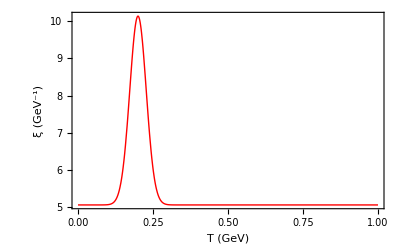

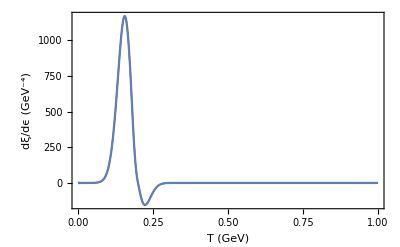

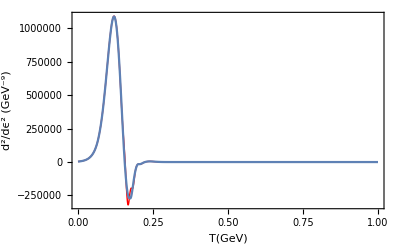

```mathematica
Clear[Cvreg,Cvsing,Cvf,dCvf]
tc=.2;

(*------------------------Subscript[c, v]------------------------*)
δ=.03;(*0.003;*) (* Small parameter to make correlation length finite at T=Subscript[T, C]. Ideally should be 0. *)
δtan=.1;(*0.09;*) 
ν=1/2; (* Critical exponent, for dependence of correlation length on (T-Subscript[T, C])/Subscript[T, C]. *)
ξhalf=0.13;  (* Correlation length at T=0.5 Subscript[T, C], in units of Subscript[T, C]^-1. It seems to like to be greater than 0.13. *)
M0=(1/ξhalf)*1/((0.5-1)^2+δ^2)^(ν/2); (*Make close to 1 or 1.1 or so on in units of Subscript[T, C]*)
M[x_]:=M0*((x-1)^2+δ^2)^(ν/2); (* Inverse correlation length in units of Subscript[T, C] *)
x0=0.86; (* Fraction of Subscript[T, C] at which the singular part of specific heat is smoothly matched to Subscript[c, V]=4AT^3. *)
Cvsing1[x_]:=ν^2*M0^3/(8π )*((x-1)^2+δ^2)^((3*ν-2)/2); 
Cvsing0[x_]:=Cvsing1[x0]*x^3/(x0^3);
Cvreg0[x_]:=x^3*1/2*(-Cvsing1[x0]/x0^3)+x^3*1/π*(Cvsing1[x0]/x0^3)*ArcTan[(x-1)/δtan];
Cvsing[x_]:=Piecewise[{{Cvsing0[x],x<x0},{Cvsing1[x],x≥x0}}]+Cvreg0[x];
Cvreg[x_?NumericQ]:=Cvreg[x]=N[4*x^3*1/2*(15.6+0.78)+4*x^3*1/π*(15.6-0.78)*ArcTan[(x-1)/δtan]];
Cvf[x_?NumericQ]:=Cvf[x]=N[Cvsing[x]+Cvreg[x]];
dCvf[t_]:=N[Cvf'[t]]

(*------------------------ T, S, P, ϵ ------------------------*)
Tlist=Table[0.01*i,{i,0,600}];
Slist=Quiet[Prepend[Flatten[Table[NIntegrate[Cvf[x]/x,{x,0.001,Tlist[[i]]}],{i,2,601}]],0]];

Sfunc=ListInterpolation[Slist,{{0.0,6}}];
Plist=Prepend[Flatten[Table[NIntegrate[Sfunc[x],{x,0.001,Tlist[[i]]}],{i,2,601}]],0];
Pfunc=ListInterpolation[Plist,{{0.0,6}}];

Epslist=Tlist*Slist-Plist;
Epsfunc=ListInterpolation[Epslist,{{0.0,6}}];

TEpslist=Thread[{Epslist*tc^4,Tlist*tc}];
TEpsfunc=Interpolation[TEpslist];

(*------------------------ Lists for EoS file ------------------------*)
(*tc=.17 -> ec = .025*)
ran=Range[.01,.6,.001];
Length[ran]
es=(Epsfunc[#]/#^4)&/@(ran/tc);
ps=(Pfunc[#]/#^4)&/@(ran/tc);
cs=(Sfunc[#]/Cvf[#])&/@(ran/tc);
(*xis=(1/(tc*M[#]))&/@(ran/tc);*)


(*------------------------ ξ, dξ/dt, (d^2 ξ)/dt^2 ------------------------*)
Clear[Δ,a1]

(*in GeV^-1*)
ξ[t_]:=(((√(t^2+Δ^2))/a1)^(-1/2)*Exp[-t^2/(.2)^2]+1)*(.1973)^-1;
dξ[t_]:=(ⅇ^(-25 t^2) t (-0.5-50 t^2-50 Δ^2))/(√((√(t^2+Δ^2))/a1) (t^2+Δ^2))*(.1973)^-1;
ddξ[t_]:=(.1973)^-1/(√((√(t^2+Δ^2))/a1) (t^2+Δ^2)^3)ⅇ^(-25 t^2) (2500 t^8+7500 t^6 Δ^2-0.5 Δ^4-50 Δ^6+t^4 (0.75-50 Δ^2+7500 Δ^4)+t^2 (0.25 Δ^2-100 Δ^4+2500 Δ^6));

tvsT[T_]:=(T-tc)/tc;
ξvsT[T_]:=ξ[tvsT[T]];
dξvsT[T_]:=dξ[tvsT[T]];
ddξvsT[T_]:=ddξ[tvsT[T]];

ξmax=2;{a1,Δ}={0.4,(a1(ξmax-1)^-2)};


(*------------------------dξ/dϵ------------------------*)
dξdϵ[t_]:=dξ[t]/Cvf[t+1];
xlist={.06,.07};
data=Table[Log[dξdϵ[tvsT[T]]]/.T->elm,{elm,xlist}];

α=(data⟦2⟧-data⟦1⟧)/(xlist⟦2⟧-xlist⟦1⟧)
c = α*xlist⟦1⟧-data⟦1⟧

dξdϵvsT[T_]:=If[T>xlist⟦2⟧,dξdϵ[tvsT[T]],Exp[α*T-c]]


(*------------------------(d^2 ξ)/dϵ^2------------------------*)
xlist2={.06,.07};
data=Table[Log[(1/Cvf[T/tc]^2(ddξvsT[T]-dCvf[T/tc]/Cvf[T/tc] dξvsT[T]))]/.T->elm,{elm,xlist2}];

α2=(data⟦2⟧-data⟦1⟧)/(xlist2⟦2⟧-xlist2⟦1⟧)
c2 = α2*xlist2⟦1⟧-data⟦1⟧

d2ξdϵ2vsT[T_]:=If[T>xlist2⟦2⟧,1/Cvf[T/tc]^2(ddξvsT[T]-dCvf[T/tc]/Cvf[T/tc] dξvsT[T]),Exp[α2*T-c2]];

Plot[ξvsT[t],{t,0,1},PlotRange->All,Frame->True,Axes->False,PlotStyle->{Red,Thick},FrameLabel->{Style["T (GeV)",16],Style["ξ (GeV^-1)",16]},LabelStyle->Medium]

Show[{Plot[dξdϵvsT[t]/tc^4,{t,0,1},PlotRange->All,Frame->True,Axes->False,PlotStyle->{Red,Thick},FrameLabel->{"T (GeV)","dξ/dϵ (GeV^-4)"},LabelStyle->Medium],
Plot[D[ξvsT[TEpsfunc[eps]],eps]/.eps->(Epsfunc[t/tc]*tc^4),{t,0,1},PlotRange->All]}]

Show[Plot[d2ξdϵ2vsT[t]/tc^8,{t,0,1},PlotRange->All,Frame->True,Axes->False,PlotStyle->{Red,Thick},FrameLabel->{"T(GeV)","d^2/dϵ^2 (GeV^-9)"},LabelStyle->Medium],
Plot[func2p2[t],{t,0,1},PlotRange->All]]


xis=ξvsT/@(ran);
dXis=(func1)/@(ran);
d2Xi=(func2p2)/@(ran);
(*dXis=(dξdϵvsT[#]/tc^4)&/@(ran);
d2Xi=(d2ξdϵ2vsT[#]/tc^8)&/@(ran);*)
cvs = (Cvf[#])&/@(ran/tc);
```

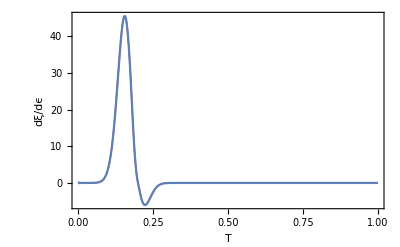

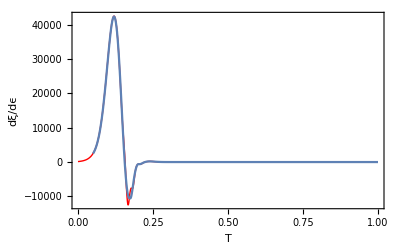

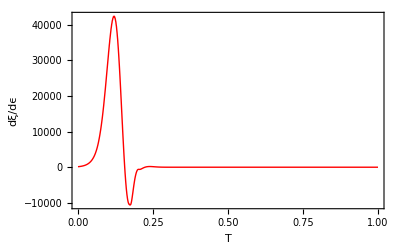

```mathematica
func1[t_]:=D[ξvsT[TEpsfunc[eps]],eps]/.eps->(Epsfunc[t/tc]*tc^4);
func2[t_]:=D[func1[TEpsfunc[eps]],eps]/.eps->(Epsfunc[t/tc]*tc^4);
func2p2[t_]:=If[t<.1,d2ξdϵ2vsT[t]/tc^8,func2[t]];


Show[{Plot[dξdϵvsT[t]/tc^4,{t,0,1},PlotRange->All,Frame->True,Axes->False,PlotStyle->{Red,Thick},FrameLabel->{"T","dξ/dϵ"},LabelStyle->Medium],
Plot[func1[t],{t,0,1},PlotRange->All]}]

Show[{Plot[d2ξdϵ2vsT[t]/tc^8,{t,0,1},PlotRange->All,Frame->True,Axes->False,PlotStyle->{Red,Thick},FrameLabel->{"T","dξ/dϵ"},LabelStyle->Medium],
Plot[func2[t],{t,0.05,1},PlotRange->All]}]

Plot[func2p2[t],{t,0,1},PlotRange->All,Frame->True,Axes->False,PlotStyle->{Red,Thick},FrameLabel->{"T","dξ/dϵ"},LabelStyle->Medium]
```

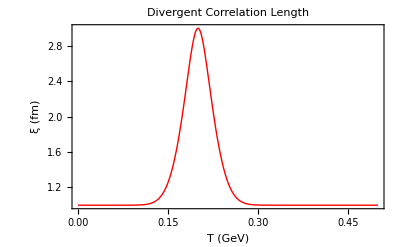

```mathematica
xiPlt=Plot[ξvsT[t],{t,0,0.5},PlotRange->All,Frame->True,Axes->False,
PlotStyle->{Red,Thick},
PlotLabel->Style["Divergent Correlation Length",20],
FrameLabel->{Style["T (GeV)",20],Style["ξ (fm)",20]}]
```

```mathematica
Export["/Users/GregoryRidgway/Desktop/RHIC and Hydro/Talks/xiPlt.png",xiPlt]
```

/Users/GregoryRidgway/Desktop/RHIC and Hydro/Talks/xiPlt.png

```mathematica
data=Transpose[SetPrecision[{ran,es,ps,cs,xis, dXis,d2Xi,cvs},8]];
Export["/Users/GregoryRidgway/Desktop/RHIC and Hydro/SimulatingHydroPlus/gregRyanEOS.dat",data]
```

/Users/GregoryRidgway/Desktop/RHIC and Hydro/SimulatingHydroPlus/gregRyanEOS.dat

Plots

```mathematica
Plot[Sfunc[T]/T^3,{T,0.001,6},PlotLabel->"s/T^3 vs. T/T_C",AxesLabel->{"T/T_C","s/T^3"}]
Plot[Pfunc[T]/T^4,{T,0.01,6},PlotLabel->"p/T^4 vs. T/T_C",AxesLabel->{"T/T_C","p/T^4"}]
```

```mathematica
Plot[Epsfunc[T]/T^4,{T,0.01,6},PlotLabel->"ϵ/T^4 vs. T/T_C",AxesLabel->{"T/T_C","ϵ/T^4"},PlotRange->All]
plotCs=Plot[Sfunc[T]/Cvf[T],{T,0.01,6},PlotRange->All,PlotLabel->"c_s^2 vs. T/T_C",AxesLabel->{"T/T_C","c_s^2"}];
plotCsConf=Plot[1/3,{T,0.0,6},PlotRange->{0,0.4},PlotStyle->{Gray,Dashed},PlotLegends->{"Conformal Fluid"}];
Show[plotCs,plotCsConf,GridLines->{{{0.86,{Black,Dashed}},{1,Black},{1.14,{Black,Dashed}}},None}]
```

```mathematica
plot1=Plot[Cvf[T]/T^3,{T,0,2.5},PlotRange->{0,100},PlotLabel->"c_v/T^3 vs. T/T_C",AxesLabel->{"T/T_C","c_v/T^3"},PlotLegends->{"Combined"}];
plot2=Plot[Cvsing[T]/T^3,{T,0,2.5},PlotRange->{0,100},PlotStyle->{Red},PlotLegends->{"Singular"}];
plot3=Plot[Cvreg[T]/T^3,{T,0,2.5},PlotRange->{0,100},PlotStyle->{Green},PlotLegends->{"Regular"}];
Show[plot1,plot2,plot3,GridLines->{{{0.86,{Black,Dashed}},{1,{Black}},{1.14,{Black,Dashed}}},None}]
```

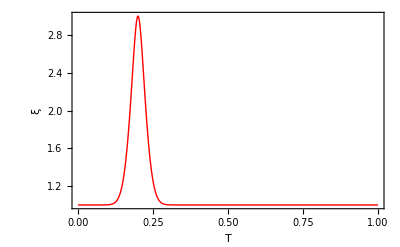

```mathematica
Plot[ξvsT[T],{T,0,1},PlotRange->All,Frame->True,Axes->False,PlotStyle->{Red,Thick},FrameLabel->{"T","ξ"},LabelStyle->Medium]
```

114.44

14.3176

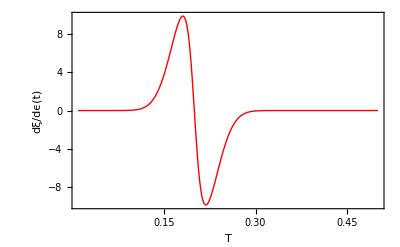

Differences[xlist]

```mathematica
dξdϵ[t_]:=dξ[t]/Cvf[t+1];

xlist={.06,.07};
data=Table[Log[dξdϵ[tvsT[T]]]/.T->elm,{elm,xlist}];

α=(data⟦2⟧-data⟦1⟧)/(xlist⟦2⟧-xlist⟦1⟧)
c = α*xlist⟦1⟧-data⟦1⟧

dξdϵvsT[T_]:=If[T>xlist⟦2⟧,dξdϵ[tvsT[T]],Exp[α*T-c]]

Plot[dξvsT[T],{T,.01,.5},PlotRange->All,Frame->True,Axes->False,PlotStyle->{Red,Thick},FrameLabel->{"T","dξ/dϵ(t)"},LabelStyle->Medium]
```

{-2.78773,-2.20452}

58.3215

6.28702

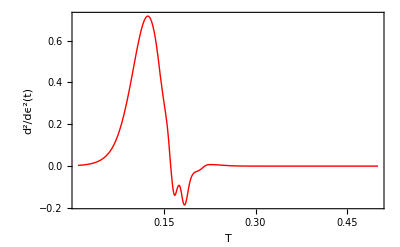

```mathematica
xlist={.06,.07};
data=Table[Log[(1/Cvf[T/tc]^2(ddξvsT[T]-dCvf[T/tc]/Cvf[T/tc] dξvsT[T]))]/.T->elm,{elm,xlist}]

α2=(data⟦2⟧-data⟦1⟧)/(xlist⟦2⟧-xlist⟦1⟧)
c2 = α2*xlist⟦1⟧-data⟦1⟧

d2ξdϵ2vsT[T_]:=If[T>xlist⟦2⟧,1/Cvf[T/tc]^2(ddξvsT[T]-dCvf[T/tc]/Cvf[T/tc] dξvsT[T]),Exp[α2*T-c2]];
Plot[d2ξdϵ2vsT[T],{T,.01,.5},PlotRange->All,Frame->True,Axes->False,PlotStyle->{Red,Thick},FrameLabel->{"T","d^2/dϵ^2(t)"},LabelStyle->Medium]
```

```mathematica
Exp[data[[1]]]
```

0.0134355

Scratch

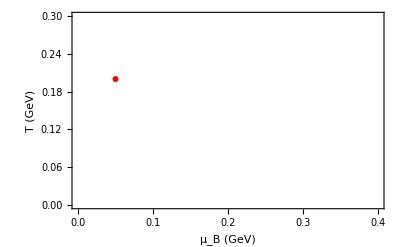

/Users/GregoryRidgway/Desktop/RHIC and Hydro/Paul Stuff/PhaseDiagram.png

```mathematica
plt1=ListPlot[{{.05,.2}},PlotRange->{{0,.4},{0,.3}},PlotMarkers->{"X",20},PlotStyle->Red,FrameLabel->{Style["μ_B (GeV)",16],Style["T (GeV)",16]}]
Export["/Users/GregoryRidgway/Desktop/RHIC and Hydro/Paul Stuff/PhaseDiagram.png",plt1]
```